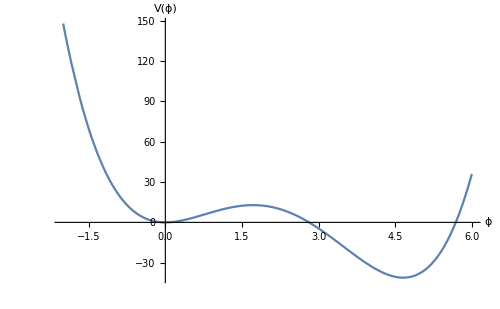

```mathematica
Plot[x^2(x-4)^2-.5x^3,{x,-2,6},AxesLabel->{Style["ϕ",Bold,16],Style["V(ϕ)",Bold,16]},Frame->False,Axes->True,Ticks->None]
```

# Electroweak baryogenesis at high wall velocities (arXiv:2001.00568)

```mathematica
ClearAll["Global`*"];SetDirectory[NotebookDirectory[]];
SetOptions[{ParametricPlot,ListLinePlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot,ListContourPlot,LogPlot,Plot,RegionPlot,ContourPlot},Frame->True,BaseStyle->{FontColor->Black,FontWeight->"Normal",FontSize->16,FontFamily->"Times"},Axes->False,PlotLegends->Automatic,AspectRatio->1,ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->Full];
colours=ColorData[97,"ColorList"];
WP=MachinePrecision;T=100;(*Fiducial value for the nucleation temperature*);
v0=0.01;
v0=-Abs[v0](*Fiducial value for wall speed*);
```

## Definitions from Appendix A

In the following formulas the variable “w” represents the WKB energy, “vw” is the wall velocity

```mathematica
β=1/T;
pw=√(w^2-x^2);(*Formula defined after A3*)
pz=1/(√(1-vw^2))(y pw-w vw);(*Formula defined after A3*)
Eb=1/(√(1-vw^2))(w-vw y pw);(*Formula defined after A3*)
Vs = √(pz^2)/√(pz^2+x^2);(*Formula  A4*)
Vh=Vs^2 1/(√(1-x^2/Eb^2));(*Formula  A5*);
ff=1/(Exp[β w]+1);(*Distribution funcion for fermion *)
fb=1/(Exp[β w]-1);(*Distribution funcion for boson *)
ff1=D[ff,w];(*Derivative of Distribution funcion for fermion *)
fb1=D[fb,w];(*Derivative of Distribution funcion for boson *)
ff2=D[ff1,w];(*Second Derivative of Distribution funcion for fermion *)
fb2=D[fb1,w];(*Second Derivative of Distribution funcion for boson *)
```

## Field Profiles

```mathematica
h[z_]:=h0/2(Tanh[z/Lh]+1)/.{h0->T,Lh->5/T}(**equation (50) LEFT MOVING WALL!!**)
s[z_]:=s0/2(1-Tanh[z/Ls-δs])/.{s0->2 T,Ls->5/T,δs->0}(**equation (50)**)
mt[z_]:=yt/√2 h[z] √(1+s[z]^2/Λ^2)/.{Λ->1000,yt->0.99571}(**equation (49)**)
θ[z_]:=ArcTan[s[z]/Λ]/.Λ->1000(**equation (49)**)
mb[z_]:=4.2*h[z]/h0 /.{h0->T}
mh[z_]:=125.3*h[z]/h0 /.{h0->T}
```

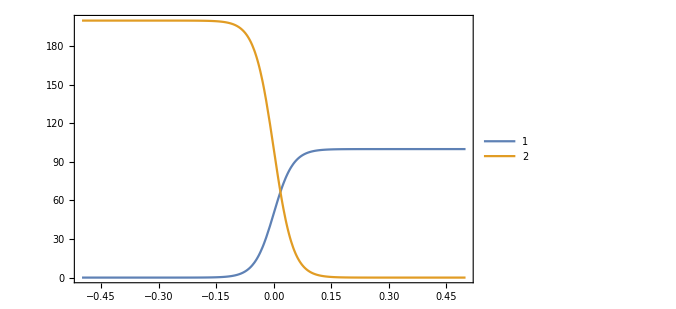

```mathematica
Plot[{h[z],s[z]},{z,-0.5,0.5}]
```

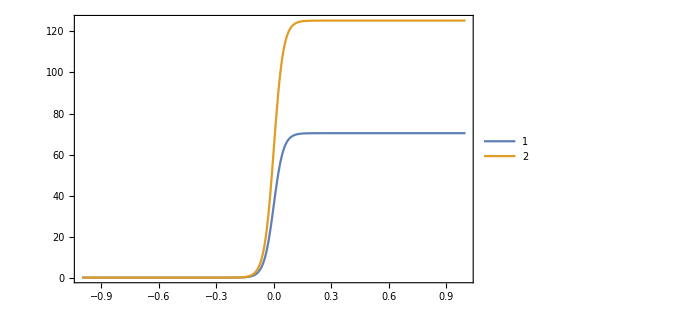

```mathematica
Plot[{mt[z],mh[z]},{z,-1,1}]
```

## Coefficients Helicity Eigenstates

K_0 (Formula (43))

```mathematica
Kf0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2 NIntegrate[pw Eb ff/.{x->xi,vw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for fermions*);
Kb0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb/.{x->xi,vw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for bosons*);
```

```mathematica
Kf0inter=Interpolation[Table[{x,Kf0[x,v0]},{x,0,130,10}]];
Kb0inter=Interpolation[Table[{x,Kb0[x,v0]},{x,0,130,10}]];
```

```mathematica
K0t[z_]:=Kf0inter[mt[z]];
K0b[z_]:=Kf0inter[mb[z]];
K0h[z_]:=Kb0inter[mh[z]];
```

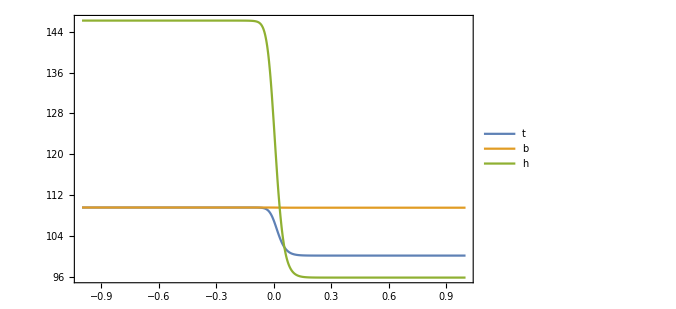

```mathematica
Plot[{K0t[z],K0b[z],K0h[z]},{z,-1,1},PlotLegends->{"t","b","h"},PlotRange->Full]
```

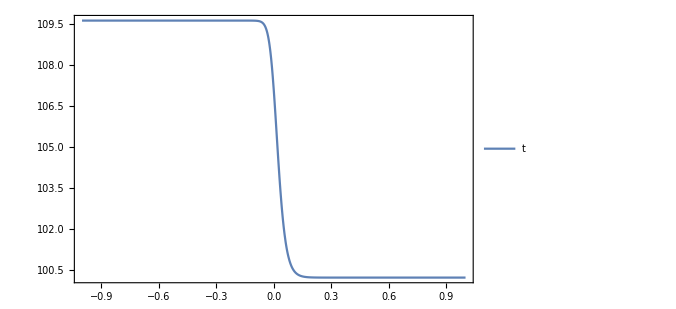

```mathematica
Plot[K0t[z],{z,-1,1},PlotLegends->{"t"},PlotRange->Full]
```

D_0 (Formula (26))

```mathematica
Df0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb ff1/.{x->xi,vw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=0*);
Db0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb1/.{x->xi,vw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=0*);
```

```mathematica
Df0inter=Interpolation[Table[{x,Df0[x,v0]},{x,0,130,10}]];
Db0inter=Interpolation[Table[{x,Db0[x,v0]},{x,0,130,10}]];
```

```mathematica
D0t[z_]:=Df0inter[mt[z]];
D0b[z_]:=Df0inter[mb[z]];
D0h[z_]:=Db0inter[mh[z]];
```

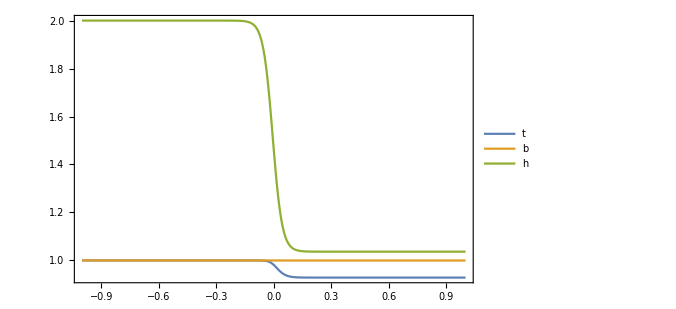

```mathematica
Plot[{D0t[z],D0b[z],D0h[z]},{z,-1,1},PlotLegends->{"t","b","h"},PlotRange->Full]
```

D_1 (Formula (26))

```mathematica
Df1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz ff1/.{x->xi,vw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=1*);
Db1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz fb1/.{x->xi,vw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=1*);
Df1inter=Interpolation[Table[{x,Df1[x,v0]},{x,0,130,10}]];
Db1inter=Interpolation[Table[{x,Db1[x,v0]},{x,0,130,10}]];
D1t[z_]:=Df1inter[mt[z]];
D1b[z_]:=Df1inter[mb[z]];
D1h[z_]:=Db1inter[mh[z]];
```

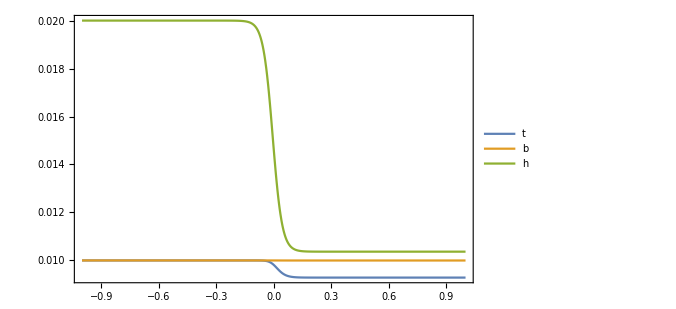

```mathematica
Plot[{D1t[z],D1b[z],D1h[z]},{z,-1,1},PlotLegends->{"t","b","h"},PlotRange->Full]
```

D_2 (Formula (26))

```mathematica
Df2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb ff1/.{x->xi,vw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=2*);
Db2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb fb1/.{x->xi,vw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=2*);Df2inter=Interpolation[Table[{x,Df2[x,v0]},{x,0,130,10}]];
Db2inter=Interpolation[Table[{x,Db2[x,v0]},{x,0,130,10}]];
D2t[z_]:=Df2inter[mt[z]];
D2b[z_]:=Df2inter[mb[z]];
D2h[z_]:=Db2inter[mh[z]];
```

```mathematica
Db2[0,v0]
```

0.666773

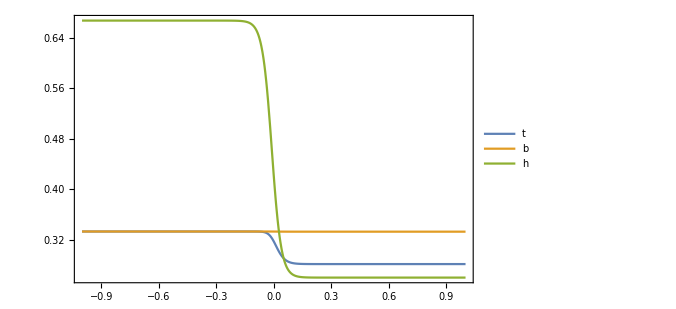

```mathematica
Plot[{D2t[z],D2b[z],D2h[z]},{z,-1,1},PlotLegends->{"t","b","h"},PlotRange->Full]
```

Q_1 (Formula (27)) Singularities arise

```mathematica
Qf1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[pw  ff2/.{x->xi,vw->vi},{y,-1,1},{w,xi,∞}](*Formula (27) for fermions, l=1*);
Qb1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[pw  fb2/.{x->0,vw->vi},{y,-1,1}],{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw  fb2/.{x->xi,vw->vi},{y,-1,1},{w,xi,∞},WorkingPrecision->10]](*Formula (27) for bosons, l=1*);
Qf1inter=Interpolation[Table[{x,Qf1[x,v0]},{x,0,130,10}]];
Qb1inter=Interpolation[Table[{x,Qb1[x,v0]},{x,0,130,10}]];
Q1t[z_]:=Qf1inter[mt[z]];
Q1b[z_]:=Qf1inter[mb[z]];
Q1h[z_]:=Qb1inter[mh[z]];
```

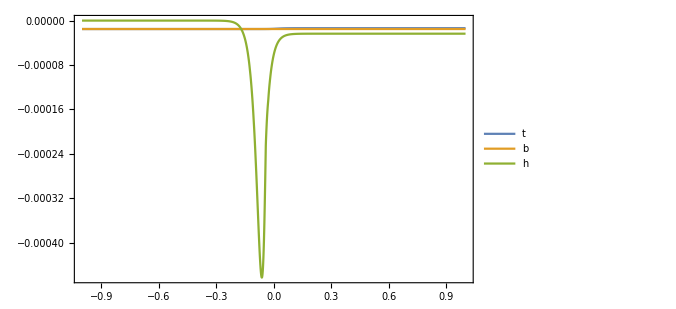

```mathematica
Plot[{Q1t[z],Q1b[z],Q1h[z]},{z,-1,1},PlotLegends->{"t","b","h"},PlotRange->Full]
```

Q_2 (Formula (27))

```mathematica
Qf2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[(pw pz)/Eb ff2/.{x->xi,vw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10](*Formula (27) for fermions, l=2*);
Qb2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[(pw pz)/Eb fb2/.{x->xi,vw->vi},{y,-1,1}],{w,xi,∞,xi},Method->PrincipalValue],NIntegrate[(pw pz)/Eb fb2/.{x->xi,vw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (27) for bosons, l=2*);
```

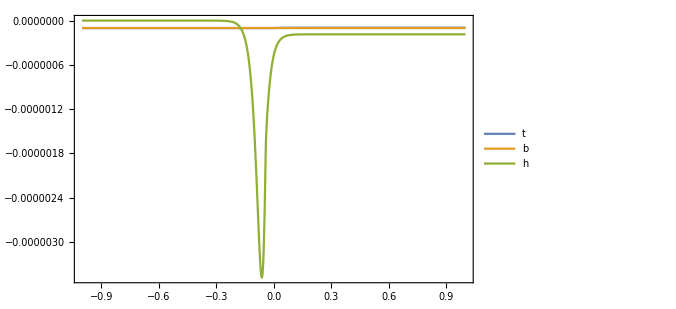

```mathematica
Qf2inter=Interpolation[Table[{x,Qf2[x,v0]},{x,0,130,10}]];
Qb2inter=Interpolation[Table[{x,Qb2[x,v0]},{x,0,130,10}]];
Q2t[z_]:=Qf2inter[mt[z]];
Q2b[z_]:=Qf2inter[mb[z]];
Q2h[z_]:=Qb2inter[mh[z]];
Plot[{Q2t[z],Q2b[z],Q2h[z]},{z,-1,1},PlotLegends->{"t","b","h"},PlotRange->Full]
```

Q_1^.1d8odd (formula (40))

```mathematica
Q1fo8integrand=FullSimplify[(Integrate[pw/pz Vh ff1/.{x->0,vw->vi},y]/.{y->1})-(Integrate[pw/pz Vh ff1/.{x->0,vw->vi},y]/.{y->-1})];Q1bo8integrand=FullSimplify[(Integrate[pw/pz Vh fb1/.{x->0,vw->vi},y]/.{y->1})-(Integrate[pw/pz Vh fb1/.{x->0,vw->vi},y]/.{y->-1})];Q1fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh ff1/.{x->xi,vw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=1, helicity eigenstates*)
Q1bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh fb1/.{x->xi,vw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=1, helicity eigenstates*);
```

```mathematica
Q1fo8inter=Interpolation[Table[{x,Q1fo8[x,v0]},{x,0,130,10}]];
Q1bo8inter=Interpolation[Table[{x,Q1bo8[x,v0]},{x,0,130,10}]];
Q1o8t[z_]:=Q1fo8inter[mt[z]];
Q1o8b[z_]:=Q1fo8inter[mb[z]];
Q1o8h[z_]:=Q1bo8inter[mh[z]];
```

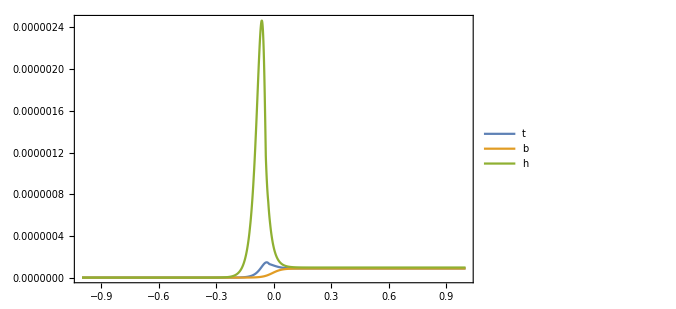

```mathematica
Plot[{Q1o8t[z],Q1o8b[z],Q1o8h[z]},{z,-1,1},PlotLegends->{"t","b","h"},PlotRange->Full]
```

Q_2^.1d8odd (formula (40))

```mathematica
Q2fo8integrand=FullSimplify[(Integrate[pw/Eb Vh ff1/.{x->0,vw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh ff1/.{x->0,vw->vi},y]/.{y->-1})];Q2bo8integrand=FullSimplify[(Integrate[pw/Eb Vh fb1/.{x->0,vw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh fb1/.{x->0,vw->vi},y]/.{y->-1})];Q2fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh ff1/.{x->xi,vw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=2, helicity eigenstates*)
Q2bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh fb1/.{x->xi,vw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=2, helicity eigenstates*);Q2fo8inter=Interpolation[Table[{x,Q2fo8[x,v0]},{x,0,130,10}]];
Q2bo8inter=Interpolation[Table[{x,Q2bo8[x,v0]},{x,0,130,10}]];
Q2o8t[z_]:=Q2fo8inter[mt[z]];
Q2o8b[z_]:=Q2fo8inter[mb[z]];
Q2o8h[z_]:=Q2bo8inter[mh[z]];
```

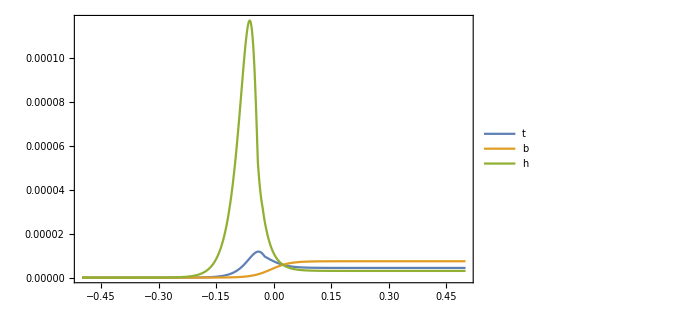

```mathematica
Plot[{Q2o8t[z],Q2o8b[z],Q2o8h[z]},{z,-0.5,0.5},PlotLegends->{"t","b","h"},PlotRange->Full]
```

Q_1^.1d9odd (formula (41))

```mathematica
Q1fo9integrand=FullSimplify[(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vw->vi},y]/.{y->1})-(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vw->vi},y]/.{y->-1})];
```

```mathematica
Q1fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q1fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->xi,vw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (41), l=1, helicity eigenstates*);
```

```mathematica
Q1fo9nter=Interpolation[Table[{x,Q1fo9[x,v0]},{x,0,130,10}]];
Q1o9t[z_]:=Q1fo9nter[mt[z]];
Q1o9b[z_]:=Q1fo9nter[mb[z]];
```

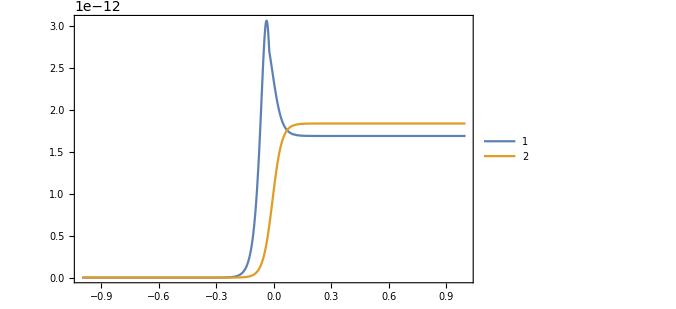

```mathematica
Plot[{Q1o9t[z],Q1o9b[z]},{z,-1,1}]
```

Q_2^.1d9odd (formula (41))

```mathematica
Q2fo9integrand=FullSimplify[(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vw->vi},y]/.{y->1})-(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vw->vi},y]/.{y->-1})];
```

```mathematica
Q2fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q2fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->xi,vw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (41) for fermions, l=2, helicity eigenstates*);Q2fo9inter=Interpolation[Table[{x,Q2fo9[x,v0]},{x,0,130,10}]];Q2o9t[z_]:=Q2fo9inter[mt[z]];
Q2o9b[z_]:=Q2fo9inter[mb[z]];
```

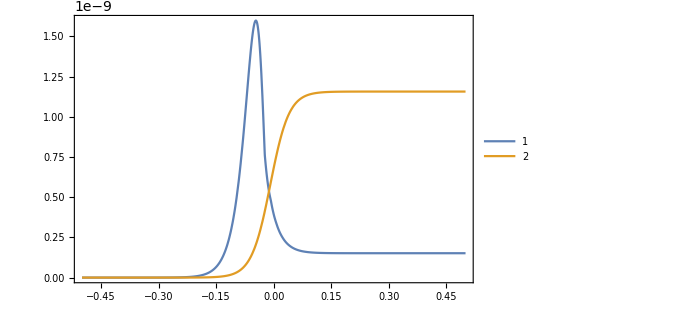

```mathematica
Plot[{Q2o9t[z],Q2o9b[z]},{z,-0.5,0.5},PlotRange->Full]
```

## Sources

```mathematica
St1[zz_]:=Evaluate[-v0/(√(1-v0^2))(D[mt[z]^2 D[θ[z],z],z]Q1o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q1o9t[z])/.{z->zz}];Sb1[zz_]:=Evaluate[-v0/(√(1-v0^2))(D[mb[z]^2 D[θ[z],z],z]Q1o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q1o9b[z])/.{z->zz}];St2[zz_]:=Evaluate[-v0/(√(1-v0^2))(D[mt[z]^2 D[θ[z],z],z]Q2o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q2o9t[z])/.{z->zz}];Sb2[zz_]:=Evaluate[-v0/(√(1-v0^2))(D[mb[z]^2 D[θ[z],z],z]Q2o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q2o9b[z])/.{z->zz}];
```

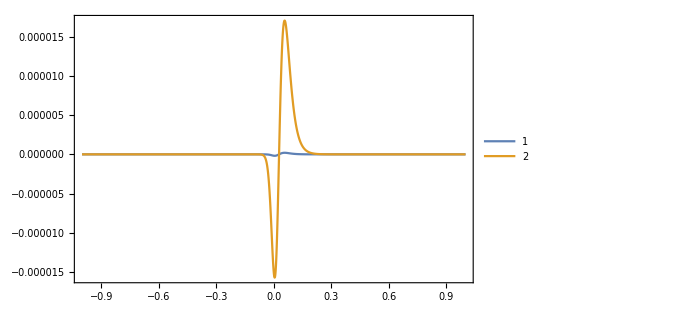

```mathematica
Plot[{Sb1[x],Sb2[x]},{x,-1,1},PlotRange->All]
```

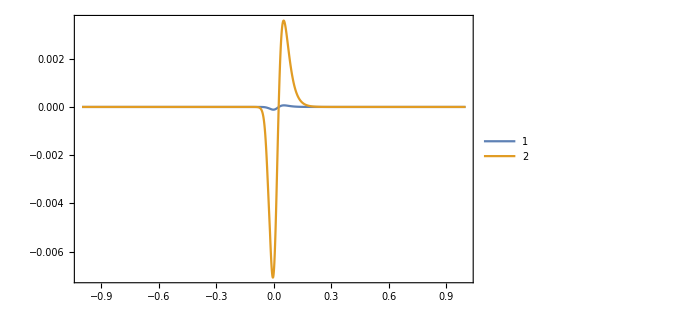

```mathematica
Plot[{St1[x],St2[x]},{x,-1,1},PlotRange->All]
```

## Collision Terms

```mathematica
δCtL1[z_]:=β K0t[z] (Γy(μtl[z]-μtr[z]+μh[z])+Γm[z](μtl[z]-μtr[z])+Γhtot[z](μtl[z]-μbl[z])+ ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]))(*Formula (53), we divide by T to get dimensions right*);δCtL2[z_]:=(-Γttot[z]utl[z]-v0 δCtL1[z]);
δCbL1[z_]:=β K0b[z](Γy(μbl[z]-μtr[z]+μh[z])+Γhtot[z](μbl[z]-μtl[z])+ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));δCbL2[z_]:=(-Γbtot[z]ubl[z]-v0 δCbL1[z]);δCtR1[z_]:=β K0t[z](-Γy(μtl[z]+μbl[z]-2μtr[z]+2μh[z])-Γm[z](μtl[z]-μtr[z])-ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));
δCtR2[z_]:=(-Γttot[z]utr[z]-v0 δCtR1[z]);
δCh1[z_]:=β K0h[z]( Γy (μtl[z]+μbl[z]-2μtr[z]+2μh[z])+Γh[z] μh[z]);
δCh2[z_]:=(-Γhtot[z]uh[z]-v0 δCh1[z]);
```

## Sphaleron Rates and Interaction Rates

```mathematica
Γsph=10^-6 T;
ΓSS=4.9*10^-4 T;
Γy=4.2*10^-3 T;
Γm[z_]:=mt[z]^2/(63 T);
mW[z_]:=g h[z]/2 /.g->0.65(*W boson mass*);
Γh[z_]:=mW[z]^2/(50T);
Dq=6/T(*quark diffusion constant*);
Dh=20/T(*higgs diffusion constant*);Γhtot[z_]:=D2h[z]/(Dh D0h[z])(*W scattering rate. This was not provided in the paper and we took it directly from ref [47] 0605242*);Γttot[z_]:=D2t[z]/(Dq D0t[z]);
Γbtot[z_]:=D2b[z]/(Dq D0b[z]);
```

## Differential Equation

```mathematica
{htl,htr,hbl}={-1,1,-1};TopLeft1={-D1t[z] μtl'[z]+utl'[z]+D[(mt[z])^2,z] v0/(√(1-v0^2)) Q1t[z] μtl[z]-δCtL1[z]==htl St1[z]};TopLeft2={-D2t[z] μtl'[z]-v0 utl'[z]+D[(mt[z])^2,z] v0/(√(1-v0^2)) Q2t[z] μtl[z]-δCtL2[z]== htl St2[z]};
BottomLeft1={-D1b[z] μbl'[z]+ubl'[z]+ D[(mb[z])^2,z] v0/(√(1-v0^2))Q1b[z] μbl[z]-δCbL1[z]==hbl Sb1[z]};BottomLeft2={-D2b[z] μbl'[z]-v0 ubl'[z]+D[(mb[z])^2,z] v0/(√(1-v0^2)) Q2b[z] μbl[z]-δCbL2[z]==hbl Sb2[z]};TopRight1={-D1t[z] μtr'[z]+utr'[z]+ D[(mt[z])^2,z] v0/(√(1-v0^2))Q1t[z] μtr[z]-δCtR1[z]==htr St1[z]};TopRight2={-D2t[z] μtr'[z]-v0 utr'[z]+D[(mt[z])^2,z] v0/(√(1-v0^2)) Q2t[z] μtr[z]-δCtR2[z]==htr St2[z]};Higgs1={-D1h[z] μh'[z]+uh'[z]+ D[(mh[z])^2,z] v0/(√(1-v0^2))Q1h[z] μh[z]-δCh1[z]==0};
Higgs2={-D2h[z] μh'[z]-v0 uh'[z]+D[(mh[z])^2,z] v0/(√(1-v0^2)) Q2h[z] μh[z]-δCh2[z]==0};
Bond={ μtl[1]==0,μtr[1]==0,μbl[1]==0,μh[1]==0, μtl[-1]==0,μtr[-1]==0,μbl[-1]==0,μh[-1]==0};Equation=Join[TopLeft1,TopLeft2,TopRight1,TopRight2,BottomLeft1,BottomLeft2,Higgs1,Higgs2,Bond];sol=NDSolve[Equation,{μtl,μtr,μbl,μh, utl,utr,ubl,uh},{z,-1,1},Method->{"Shooting",Method->"StiffnessSwitching"},MaxStepSize->0.01]
```

{{μtl→InterpolatingFunction[…],μtr→InterpolatingFunction[…],μbl→InterpolatingFunction[…],μh→InterpolatingFunction[…],utl→InterpolatingFunction[…],utr→InterpolatingFunction[…],ubl→InterpolatingFunction[…],uh→InterpolatingFunction[…]}}

```mathematica
μtlsol[z_]:=μtl[z]/.sol[[1]][[1]];μtrsol[z_]:=μtr[z]/.sol[[1]][[2]];μblsol[z_]:=μbl[z]/.sol[[1]][[3]];μhsol[z_]:=μh[z]/.sol[[1]][[4]];
```

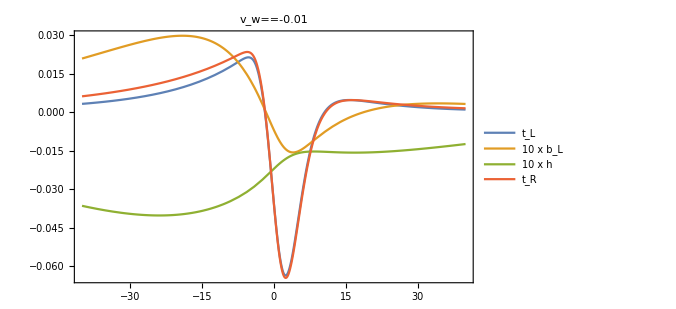

```mathematica
Plot[{μtlsol[z/T]10^4 β,μblsol[z/T]10 10^4 β,μhsol[z/T]10 10^4 β,-μtrsol[z/T]10^4 β},{z,-40,40},PlotRange->Full,PlotLegends->{"t_L","10 x b_L","10 x h","t_R"},PlotLabel->Subscript[v, w]==v0]
```

## BAU

```mathematica
μBL[z_]:=1/2(1+4D0t[z])μtlsol[z]+1/2(1+4D0b[z])μblsol[z]+2 D0t[z] μtrsol[z];
fsph[z_]:=Min[{1,2.5 T/Γsph Exp[-40 h[z]/T]}];
gdof=106.75;ηB=405 Γsph/(4π^2 v0 gdof T)√(1-v0^2) NIntegrate[μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[v0])√(1-v0^2)],{z,-1,1}]
```

-1.64374×10^-10

```mathematica
Table[v0=i;ηB=405 Γsph/(4π^2 v0 gdof T)√(1-v0^2) NIntegrate[μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 v0)√(1-v0^2)],{z,-1,1}];ηB,{i,10^-6,1,0.075}]
```

{-1.79863×10^-10,1.83423×10^-10,9.14416×10^-11,6.01915×10^-11,4.42402×10^-11,3.4414×10^-11,2.76379×10^-11,2.25843×10^-11,1.85792×10^-11,1.52343×10^-11,1.22936×10^-11,9.55037×10^-12,6.75352×10^-12,3.17857×10^-12}

```mathematica
Table[i,{i,10^-6,1,0.075}]
```

{1.×10^-6,0.075001,0.150001,0.225001,0.300001,0.375001,0.450001,0.525001,0.600001,0.675001,0.750001,0.825001,0.900001,0.975001}

```mathematica
v0=  0.150001;ηB=405 Γsph/(4π^2 v0 gdof T)√(1-v0^2) NIntegrate[μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 v0)√(1-v0^2)],{z,-1,1}]
```

9.14416×10^-11

## Bubble-Wall Data

```mathematica
ClearAll["Global`*"];SetDirectory[NotebookDirectory[]];
SetOptions[{ParametricPlot,ListLinePlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot,ListContourPlot,LogPlot,Plot,RegionPlot,ContourPlot},Frame->True,BaseStyle->{FontColor->Black,FontWeight->"Normal",FontSize->16,FontFamily->"Times"},Axes->False,PlotLegends->Automatic,AspectRatio->1,ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->Full];
colours=ColorData[97,"ColorList"];
WP=MachinePrecision;
```

```mathematica
params3=Import["root_sols_ms_80_all_1.csv","Dataset","HeaderLines"->1];
```

```mathematica
Tnlist=params3[All,"Tnuc"];
vwlist=params3[All,"vw"];
h0list=params3[All,"h0"];
Lhlist=params3[All,"Lh"];
s0list=params3[All,"s0"];
Lslist=params3[All,"Ls"];
dslist=params3[All,"ds"];
```

## Master Code Functions For Interpolation

```mathematica
ClearAll["Global`*"];SetDirectory[NotebookDirectory[]];
SetOptions[{ParametricPlot,ListLinePlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot,ListContourPlot,LogPlot,Plot,RegionPlot,ContourPlot},Frame->True,BaseStyle->{FontColor->Black,FontWeight->"Normal",FontSize->16,FontFamily->"Times"},Axes->False,PlotLegends->Automatic,AspectRatio->1,ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->Full];
colours=ColorData[97,"ColorList"];
WP=MachinePrecision;
params3=Import["root_sols_ms_80_all.csv","Dataset","HeaderLines"->1];
Tnlist=params3[All,"Tnuc"];
vwlist=params3[All,"vw"];
h0list=params3[All,"h0"];
Lhlist=params3[All,"Lh"];
s0list=params3[All,"s0"];
Lslist=params3[All,"Ls"];
dslist=params3[All,"ds"];
MasterFunction[Tn_,vw_,h0_,Lh_,s0_,Ls_,ds_,ΛCP_,Infty_]:=Module[{ηobs=8 10^-11,β=1/Tn,Γsph=10^-6 Tn,h,s,mt,
ΓSS=4.9*10^-4 Tn,
Γy=4.2*10^-3 Tn,Dq=6/Tn(*quark diffusion constant*),
Dh=20/Tn(*higgs diffusion constant*),
inf=Infty Lh (*defines the region of interpolation/integration*)},
pw=√(w^2-x^2);(*Formula defined after A3*)
pz=1/(√(1-vw^2))(y pw-w vvw);(*Formula defined after A3*)
Eb=1/(√(1-vvw^2))(w-vvw y pw);(*Formula defined after A3*)
Vs = √(pz^2)/√(pz^2+x^2);(*Formula  A4*)
Vh=Vs^2 1/(√(1-x^2/Eb^2));(*Formula  A5*);
ff=1/(Exp[β w]+1);(*Distribution funcion for fermion *)
fb=1/(Exp[β w]-1);(*Distribution funcion for boson *)
ff1=D[ff,w];(*Derivative of Distribution funcion for fermion *)
fb1=D[fb,w];(*Derivative of Distribution funcion for boson *)
ff2=D[ff1,w];(*Second Derivative of Distribution funcion for fermion *)
fb2=D[fb1,w];(*Second Derivative of Distribution funcion for boson *)
h[z_]:=h0/2(Tanh[z/Lh]+1);(**equation (50) LEFT MOVING WALL!!**)
s[z_]:=s0/2(1-Tanh[z/Ls-ds]);(**equation (50)**)
mt[z_]:=0.99571/(√2) h[z] √(1+s[z]^2/ΛCP^2);(**equation (49)**)
θ[z_]:=ArcTan[s[z]/ΛCP];(**equation (49)**)
mb[z_]:=4.2*h[z]/h0 ;
mh[z_]:=125.3*h[z]/h0 ;
Γm[z_]:=mt[z]^2/(63 Tn);
mW[z_]:=0.65 h[z]/2 (*W boson mass*);
Γh[z_]:=mW[z]^2/(50Tn);
Xmax=Max[{mt[inf],mh[inf],mb[inf],mW[inf]}]+0.1(*Max value of x used for interpolating coefficient functions*);Kf0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2 NIntegrate[pw Eb ff/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for fermions*);
Kb0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for bosons*);
Kf0inter=Interpolation[Table[{x,Kf0[x,vw]},{x,0,Xmax,Xmax/10}]];
Kb0inter=Interpolation[Table[{x,Kb0[x,vw]},{x,0,Xmax,Xmax/10}]];
K0t[z_]:=Kf0inter[mt[z]];
K0b[z_]:=Kf0inter[mb[z]];
K0h[z_]:=Kb0inter[mh[z]];Df0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=0*);
Db0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=0*);Df0inter=Interpolation[Table[{x,Df0[x,vw]},{x,0,Xmax,Xmax/10}]];
Db0inter=Interpolation[Table[{x,Db0[x,vw]},{x,0,Xmax,Xmax/10}]];
D0t[z_]:=Df0inter[mt[z]];
D0b[z_]:=Df0inter[mb[z]];
D0h[z_]:=Db0inter[mh[z]];Df1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=1*);
Db1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=1*);
Df1inter=Interpolation[Table[{x,Df1[x,vw]},{x,0,Xmax,Xmax/10}]];
Db1inter=Interpolation[Table[{x,Db1[x,vw]},{x,0,Xmax,Xmax/10}]];
D1t[z_]:=Df1inter[mt[z]];
D1b[z_]:=Df1inter[mb[z]];
D1h[z_]:=Db1inter[mh[z]];Df2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=2*);
Db2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=2*);Df2inter=Interpolation[Table[{x,Df2[x,vw]},{x,0,Xmax,Xmax/10}]];
Db2inter=Interpolation[Table[{x,Db2[x,vw]},{x,0,Xmax,Xmax/10}]];
D2t[z_]:=Df2inter[mt[z]];
D2b[z_]:=Df2inter[mb[z]];
D2h[z_]:=Db2inter[mh[z]];Qf1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[pw  ff2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞}](*Formula (27) for fermions, l=1*);
Qb1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[pw  fb2/.{x->0,vvw->vi},{y,-1,1}],{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw  fb2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞},WorkingPrecision->10]](*Formula (27) for bosons, l=1*);
Qf1inter=Interpolation[Table[{x,Qf1[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb1inter=Interpolation[Table[{x,Qb1[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1t[z_]:=Qf1inter[mt[z]];
Q1b[z_]:=Qf1inter[mb[z]];
Q1h[z_]:=Qb1inter[mh[z]];
Qf2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[(pw pz)/Eb ff2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10](*Formula (27) for fermions, l=2*);
Qb2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{y,-1,1}],{w,xi,∞,xi},Method->PrincipalValue],NIntegrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (27) for bosons, l=2*);Qf2inter=Interpolation[Table[{x,Qf2[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb2inter=Interpolation[Table[{x,Qb2[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2t[z_]:=Qf2inter[mt[z]];
Q2b[z_]:=Qf2inter[mb[z]];
Q2h[z_]:=Qb2inter[mh[z]];
Q1fo8integrand=FullSimplify[(Integrate[pw/pz Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh ff1/.{x->0,vw->vi},y]/.{y->-1})];Q1bo8integrand=FullSimplify[(Integrate[pw/pz Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh fb1/.{x->0,vw->vi},y]/.{y->-1})];Q1fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=1, helicity eigenstates*);
Q1bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=1, helicity eigenstates*);Q1fo8inter=Interpolation[Table[{x,Q1fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1bo8inter=Interpolation[Table[{x,Q1bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o8t[z_]:=Q1fo8inter[mt[z]];
Q1o8b[z_]:=Q1fo8inter[mb[z]];
Q1o8h[z_]:=Q1bo8inter[mh[z]];Q2fo8integrand=FullSimplify[(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->-1})];Q2bo8integrand=FullSimplify[(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=2, helicity eigenstates*);
Q2bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=2, helicity eigenstates*);Q2fo8inter=Interpolation[Table[{x,Q2fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2bo8inter=Interpolation[Table[{x,Q2bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2o8t[z_]:=Q2fo8inter[mt[z]];
Q2o8b[z_]:=Q2fo8inter[mb[z]];
Q2o8h[z_]:=Q2bo8inter[mh[z]];
Q1fo9integrand=FullSimplify[(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q1fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q1fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (41), l=1, helicity eigenstates*);Q1fo9nter=Interpolation[Table[{x,Q1fo9[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o9t[z_]:=Q1fo9nter[mt[z]];
Q1o9b[z_]:=Q1fo9nter[mb[z]];
Q2fo9integrand=FullSimplify[(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q2fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->15]](*Formula (41) for fermions, l=2, helicity eigenstates*);Q2fo9inter=Interpolation[Table[{x,Q2fo9[x,vw]},{x,0,Xmax,Xmax/10}]];Q2o9t[z_]:=Q2fo9inter[mt[z]];
Q2o9b[z_]:=Q2fo9inter[mb[z]];
(*St1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q1o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q1o9t[z])/.{z->zz}];Sb1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q1o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q1o9b[z])/.{z->zz}];St2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q2o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q2o9t[z])/.{z->zz}];Sb2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q2o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q2o9b[z])/.{z->zz}];
Γhtot[z_]:=D2h[z]/(Dh D0h[z])(*W scattering rate. This was not provided in the paper and we took it directly from ref [47] 0605242*);Γttot[z_]:=D2t[z]/(Dq D0t[z]);
Γbtot[z_]:=D2b[z]/(Dq D0b[z]);
δCtL1[z_]:=β K0t[z] (Γy(μtl[z]-μtr[z]+μh[z])+Γm[z](μtl[z]-μtr[z])+Γhtot[z](μtl[z]-μbl[z])+ ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]))(*Formula (53), we divide by T to get dimensions right*);δCtL2[z_]:=(-Γttot[z]utl[z]-vw δCtL1[z]);
δCbL1[z_]:=β K0b[z](Γy(μbl[z]-μtr[z]+μh[z])+Γhtot[z](μbl[z]-μtl[z])+ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));δCbL2[z_]:=(-Γbtot[z]ubl[z]-vw δCbL1[z]);δCtR1[z_]:=β K0t[z](-Γy(μtl[z]+μbl[z]-2μtr[z]+2μh[z])-Γm[z](μtl[z]-μtr[z])-ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));
δCtR2[z_]:=(-Γttot[z]utr[z]-vw δCtR1[z]);
δCh1[z_]:=β K0h[z]( Γy (μtl[z]+μbl[z]-2μtr[z]+2μh[z])+Γh[z] μh[z]);
δCh2[z_]:=(-Γhtot[z]uh[z]-vw δCh1[z]);
{htl,htr,hbl}={-1,1,-1};TopLeft1={-D1t[z] μtl'[z]+utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q1t[z] μtl[z]-δCtL1[z]==htl St1[z]};TopLeft2={-D2t[z] μtl'[z]-vw utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtl[z]-δCtL2[z]== htl St2[z]};
BottomLeft1={-D1b[z] μbl'[z]+ubl'[z]+ D[(mb[z])^2,z] vw/(√(1-vw^2))Q1b[z] μbl[z]-δCbL1[z]==hbl Sb1[z]};BottomLeft2={-D2b[z] μbl'[z]-vw ubl'[z]+D[(mb[z])^2,z] vw/(√(1-vw^2)) Q2b[z] μbl[z]-δCbL2[z]==hbl Sb2[z]};TopRight1={-D1t[z] μtr'[z]+utr'[z]+ D[(mt[z])^2,z] vw/(√(1-vw^2))Q1t[z] μtr[z]-δCtR1[z]==htr St1[z]};TopRight2={-D2t[z] μtr'[z]-vw utr'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtr[z]-δCtR2[z]==htr St2[z]};Higgs1={-D1h[z] μh'[z]+uh'[z]+ D[(mh[z])^2,z] vw/(√(1-vw^2))Q1h[z] μh[z]-δCh1[z]==0};
Higgs2={-D2h[z] μh'[z]-vw uh'[z]+D[(mh[z])^2,z] vw/(√(1-vw^2)) Q2h[z] μh[z]-δCh2[z]==0};
Bond={ μtl[inf]==0,μtr[inf]==0,μbl[inf]==0,μh[inf]==0, μtl[-inf]==0,μtr[-inf]==0,μbl[-inf]==0,μh[-inf]==0};Equation=Join[TopLeft1,TopLeft2,TopRight1,TopRight2,BottomLeft1,BottomLeft2,Higgs1,Higgs2,Bond];sol=NDSolve[Equation,{μtl,μtr,μbl,μh, utl,utr,ubl,uh},{z,-inf,inf},Method->{"Shooting",Method->"StiffnessSwitching"},MaxStepSize->0.01];μtlsol[z_]:=μtl[z]/.sol[[1]][[1]];μtrsol[z_]:=μtr[z]/.sol[[1]][[2]];μblsol[z_]:=μbl[z]/.sol[[1]][[3]];μhsol[z_]:=μh[z]/.sol[[1]][[4]];μBL[z_]:=1/2(1+4D0t[z])μtlsol[z]+1/2(1+4D0b[z])μblsol[z]+2 D0t[z] μtrsol[z];
fsph[z_]:=Min[{1,2.5 Tn/Γsph Exp[-40 h[z]/Tn]}];
gdof=106.75;ηB=405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2) NIntegrate[μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])√(1-vw^2)],{z,-inf,inf},Method->"QuasiMonteCarlo"];
Plot1=Plot[{μtlsol[z] β,μblsol[z] β,μhsol[z] β,μtrsol[z]β},{z,-inf,inf},PlotRange->Full,PlotLegends->{"t_L"," b_L"," μ_h","t_R"},PlotLabel->Subscript[v, w]==-vw];
Return[{Plot1,ηB/ηobs}]*)
Return[1];
];
MasterOutput[i_,Λcutoff_,Infty_]:=MasterFunction[Tnlist[[i]],-vwlist[[i]],h0list[[i]],Lhlist[[i]],s0list[[i]],Lslist[[i]],dslist[[i]],Λcutoff,Infty];
MasterPars[i_]:=Print["Pars  T_n="Tnlist[[i]]," v_w=",-vwlist[[i]]," h_0=",h0list[[i]]," L_h=",Lhlist[[i]]," s_0=",s0list[[i]]," L_s",Lslist[[i]]," ds=",dslist[[i]]];
MasterPars[-1]
(*MasterOutput[-1,540,5]*)
(*vwdat=Table[vwlist[[i]],{i,1,Length[vwlist]}];*)
```

61.6611 Pars  T_n= v_w=-0.734866 h_0=231.54 L_h=0.0512598 s_0=136.414 L_s0.0512598 ds=0.710887

## Master Code (ms=100 GeV) Gamma denom

```mathematica
Abs[BAULAM540[[All,{1,4}]]]
```

{{0.32998,0.823821},{0.371708,0.834869},{0.410233,0.837885},{0.463559,0.79814},{0.51974,0.860713},{0.562252,1.12199},{0.580475,1.32234},{0.599279,1.52254},{0.618538,1.70817},{0.647985,1.96408},{0.689448,2.25751},{0.689448,2.25751},{0.692829,2.28006},{0.696514,2.30299},{0.700141,2.32599},{0.71155,2.39519}}

```mathematica
ClearAll["Global`*"];SetDirectory[NotebookDirectory[]];
SetOptions[{ParametricPlot,ListLinePlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot,ListContourPlot,LogPlot,Plot,RegionPlot,ContourPlot},Frame->True,BaseStyle->{FontColor->Black,FontWeight->"Normal",FontSize->16,FontFamily->"Times"},Axes->False,PlotLegends->Automatic,AspectRatio->1,ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->Full];
colours=ColorData[97,"ColorList"];
WP=MachinePrecision;
params3=Import["Wall_Solutions_3/ms_100_total.csv","Dataset","HeaderLines"->1];
Tnlist=params3[All,"Tnuc"];
TpoverTnlist=params3[All,"Tp/TN"];
vwlist=params3[All,"vw"];
vplist=params3[All,"vp"];
h0list=params3[All,"h0"];
Lhlist=params3[All,"Lh"];
s0list=params3[All,"s0"];
Lslist=params3[All,"Ls"];
dslist=params3[All,"ds"];
MasterFunction[Tn_,vw_,h0_,Lh_,s0_,Ls_,ds_,ΛCP_,Infty_,points_]:=Module[{ηobs=8 10^-11,β=1/Tn,Γsph=10^-6 Tn,h,s,mt,Bond,Equation,sol,μtlsol,μtrsol,μblsol,μhsol,μBL,fsph,gdof,ηB,Plot1,Plot2,
ΓSS=4.9*10^-4 Tn,
Γy=4.2*10^-3 Tn,Dq=6/Tn(*quark diffusion constant*),
Dh=20/Tn(*higgs diffusion constant*),
inf=Infty Lh (*defines the region of interpolation/integration*)},
pw=√(w^2-x^2);(*Formula defined after A3*)
pz=1/(√(1-vw^2))(y pw-w vw);(*Formula defined after A3*)
Eb=1/(√(1-vw^2))(w-vw y pw);(*Formula defined after A3*)
Vs = √(pz^2)/√(pz^2+x^2);(*Formula  A4*)
Vh=Vs^2 1/(√(1-x^2/Eb^2));(*Formula  A5*);
ff=1/(Exp[β w]+1);(*Distribution funcion for fermion *)
fb=1/(Exp[β w]-1);(*Distribution funcion for boson *)
ff1=D[ff,w];(*Derivative of Distribution funcion for fermion *)
fb1=D[fb,w];(*Derivative of Distribution funcion for boson *)
ff2=D[ff1,w];(*Second Derivative of Distribution funcion for fermion *)
fb2=D[fb1,w];(*Second Derivative of Distribution funcion for boson *)
h[z_]:=h0/2(Tanh[z/Lh]+1);(**equation (50) LEFT MOVING WALL!!**)
s[z_]:=s0/2(1-Tanh[z/Ls-ds]);(**equation (50)**)
mt[z_]:=0.99571/(√2) h[z] √(1+s[z]^2/ΛCP^2);(**equation (49)**)
θ[z_]:=ArcTan[s[z]/ΛCP];(**equation (49)**)
mb[z_]:=4.2*h[z]/h0 ;
mh[z_]:=125.3*h[z]/h0 ;
Γm[z_]:=mt[z]^2/(63 Tn);
mW[z_]:=0.65 h[z]/2 (*W boson mass*);
Γh[z_]:=mW[z]^2/(50Tn);
Xmax=Max[{mt[inf],mh[inf],mb[inf],mW[inf]}]+0.1(*Max value of x used for interpolating coefficient functions*);Kf0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2 NIntegrate[pw Eb ff/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for fermions*);
Kb0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for bosons*);
Kf0inter=Interpolation[Table[{x,Kf0[x,vw]},{x,0,Xmax,Xmax/10}]];
Kb0inter=Interpolation[Table[{x,Kb0[x,vw]},{x,0,Xmax,Xmax/10}]];
K0t[z_]:=Kf0inter[mt[z]];
K0b[z_]:=Kf0inter[mb[z]];
K0h[z_]:=Kb0inter[mh[z]];Df0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=0*);
Db0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=0*);Df0inter=Interpolation[Table[{x,Df0[x,vw]},{x,0,Xmax,Xmax/10}]];
Db0inter=Interpolation[Table[{x,Db0[x,vw]},{x,0,Xmax,Xmax/10}]];
D0t[z_]:=Df0inter[mt[z]];
D0b[z_]:=Df0inter[mb[z]];
D0h[z_]:=Db0inter[mh[z]];Df1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=1*);
Db1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=1*);
Df1inter=Interpolation[Table[{x,Df1[x,vw]},{x,0,Xmax,Xmax/10}]];
Db1inter=Interpolation[Table[{x,Db1[x,vw]},{x,0,Xmax,Xmax/10}]];
D1t[z_]:=Df1inter[mt[z]];
D1b[z_]:=Df1inter[mb[z]];
D1h[z_]:=Db1inter[mh[z]];Df2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=2*);
Db2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=2*);Df2inter=Interpolation[Table[{x,Df2[x,vw]},{x,0,Xmax,Xmax/10}]];
Db2inter=Interpolation[Table[{x,Db2[x,vw]},{x,0,Xmax,Xmax/10}]];
D2t[z_]:=Df2inter[mt[z]];
D2b[z_]:=Df2inter[mb[z]];
D2h[z_]:=Db2inter[mh[z]];Qf1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[pw  ff2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞}](*Formula (27) for fermions, l=1*);
Qb1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[pw  fb2/.{x->0,vvw->vi},{y,-1,1}],{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw  fb2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞},WorkingPrecision->10]](*Formula (27) for bosons, l=1*);
Qf1inter=Interpolation[Table[{x,Qf1[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb1inter=Interpolation[Table[{x,Qb1[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1t[z_]:=Qf1inter[mt[z]];
Q1b[z_]:=Qf1inter[mb[z]];
Q1h[z_]:=Qb1inter[mh[z]];
Qf2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[(pw pz)/Eb ff2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10](*Formula (27) for fermions, l=2*);
Qb2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{y,-1,1}],{w,xi,∞,xi},Method->PrincipalValue],NIntegrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (27) for bosons, l=2*);Qf2inter=Interpolation[Table[{x,Qf2[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb2inter=Interpolation[Table[{x,Qb2[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2t[z_]:=Qf2inter[mt[z]];
Q2b[z_]:=Qf2inter[mb[z]];
Q2h[z_]:=Qb2inter[mh[z]];
Q1fo8integrand=FullSimplify[(Integrate[pw/pz Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh ff1/.{x->0,vw->vi},y]/.{y->-1})];Q1bo8integrand=FullSimplify[(Integrate[pw/pz Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh fb1/.{x->0,vw->vi},y]/.{y->-1})];Q1fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=1, helicity eigenstates*);
Q1bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=1, helicity eigenstates*);Q1fo8inter=Interpolation[Table[{x,Q1fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1bo8inter=Interpolation[Table[{x,Q1bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o8t[z_]:=Q1fo8inter[mt[z]];
Q1o8b[z_]:=Q1fo8inter[mb[z]];
Q1o8h[z_]:=Q1bo8inter[mh[z]];Q2fo8integrand=FullSimplify[(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->-1})];Q2bo8integrand=FullSimplify[(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=2, helicity eigenstates*);
Q2bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=2, helicity eigenstates*);Q2fo8inter=Interpolation[Table[{x,Q2fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2bo8inter=Interpolation[Table[{x,Q2bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2o8t[z_]:=Q2fo8inter[mt[z]];
Q2o8b[z_]:=Q2fo8inter[mb[z]];
Q2o8h[z_]:=Q2bo8inter[mh[z]];
Q1fo9integrand=FullSimplify[(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q1fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q1fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (41), l=1, helicity eigenstates*);Q1fo9nter=Interpolation[Table[{x,Q1fo9[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o9t[z_]:=Q1fo9nter[mt[z]];
Q1o9b[z_]:=Q1fo9nter[mb[z]];
Q2fo9integrand=FullSimplify[(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q2fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->15]](*Formula (41) for fermions, l=2, helicity eigenstates*);Q2fo9inter=Interpolation[Table[{x,Q2fo9[x,vw]},{x,0,Xmax,Xmax/10}]];Q2o9t[z_]:=Q2fo9inter[mt[z]];
Q2o9b[z_]:=Q2fo9inter[mb[z]];
St1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q1o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q1o9t[z])/.{z->zz}];Sb1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q1o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q1o9b[z])/.{z->zz}];St2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q2o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q2o9t[z])/.{z->zz}];Sb2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q2o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q2o9b[z])/.{z->zz}];
Γhtot[z_]:=D2h[z]/(Dh D0h[z])(*W scattering rate. This was not provided in the paper and we took it directly from ref [47] 0605242*);Γttot[z_]:=D2t[z]/(Dq D0t[z]);
Γbtot[z_]:=D2b[z]/(Dq D0b[z]);
δCtL1[z_]:=β K0t[z] (Γy(μtl[z]-μtr[z]+μh[z])+Γm[z](μtl[z]-μtr[z])+Γhtot[z](μtl[z]-μbl[z])+ ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]))(*Formula (53), we divide by T to get dimensions right*);δCtL2[z_]:=(-Γttot[z]utl[z]-vw δCtL1[z]);
δCbL1[z_]:=β K0b[z](Γy(μbl[z]-μtr[z]+μh[z])+Γhtot[z](μbl[z]-μtl[z])+ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));δCbL2[z_]:=(-Γbtot[z]ubl[z]-vw δCbL1[z]);δCtR1[z_]:=β K0t[z](-Γy(μtl[z]+μbl[z]-2μtr[z]+2μh[z])-Γm[z](μtl[z]-μtr[z])-ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));
δCtR2[z_]:=(-Γttot[z]utr[z]-vw δCtR1[z]);
δCh1[z_]:=β K0h[z]( Γy (μtl[z]+μbl[z]-2μtr[z]+2μh[z])+Γh[z] μh[z]);
δCh2[z_]:=(-Γhtot[z]uh[z]-vw δCh1[z]);
{htl,htr,hbl}={-1,1,-1};TopLeft1={-D1t[z] μtl'[z]+utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q1t[z] μtl[z]-δCtL1[z]==htl St1[z]};TopLeft2={-D2t[z] μtl'[z]-vw utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtl[z]-δCtL2[z]== htl St2[z]};
BottomLeft1={-D1b[z] μbl'[z]+ubl'[z]+ D[(mb[z])^2,z] vw/(√(1-vw^2))Q1b[z] μbl[z]-δCbL1[z]==hbl Sb1[z]};BottomLeft2={-D2b[z] μbl'[z]-vw ubl'[z]+D[(mb[z])^2,z] vw/(√(1-vw^2)) Q2b[z] μbl[z]-δCbL2[z]==hbl Sb2[z]};TopRight1={-D1t[z] μtr'[z]+utr'[z]+ D[(mt[z])^2,z] vw/(√(1-vw^2))Q1t[z] μtr[z]-δCtR1[z]==htr St1[z]};TopRight2={-D2t[z] μtr'[z]-vw utr'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtr[z]-δCtR2[z]==htr St2[z]};Higgs1={-D1h[z] μh'[z]+uh'[z]+ D[(mh[z])^2,z] vw/(√(1-vw^2))Q1h[z] μh[z]-δCh1[z]==0};
Higgs2={-D2h[z] μh'[z]-vw uh'[z]+D[(mh[z])^2,z] vw/(√(1-vw^2)) Q2h[z] μh[z]-δCh2[z]==0};
Bond={ μtl[inf]==0,μtr[inf]==0,μbl[inf]==0,μh[inf]==0, μtl[-inf]==0,μtr[-inf]==0,μbl[-inf]==0,μh[-inf]==0};Equation=Join[TopLeft1,TopLeft2,TopRight1,TopRight2,BottomLeft1,BottomLeft2,Higgs1,Higgs2,Bond];sol=NDSolve[Equation,{μtl,μtr,μbl,μh, utl,utr,ubl,uh},{z,-inf,inf},Method->{"Shooting",Method->{"FixedStep",Method->"ExplicitEuler"}},StartingStepSize->2inf/points(*,Method->{"Shooting",Method->"StiffnessSwitching"},MaxStepSize->0.01*)];μtlsol[z_]:=μtl[z]/.sol[[1]][[1]];μtrsol[z_]:=μtr[z]/.sol[[1]][[2]];μblsol[z_]:=μbl[z]/.sol[[1]][[3]];μhsol[z_]:=μh[z]/.sol[[1]][[4]];μBL[z_]:=1/2(1+4D0t[z])μtlsol[z]+1/2(1+4D0b[z])μblsol[z]+2 D0t[z] μtrsol[z];
fsph[z_]:=Min[{1,2.5 Tn/Γsph Exp[-40 h[z]/Tn]}];
gdof=106.75;
ηB=405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2) NIntegrate[μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])√(1-vw^2)],{z,-inf,inf},Method->"QuasiMonteCarlo"];
Plot2=Plot[405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2)μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])√(1-vw^2)]/ηobs,{z,-inf,inf},FrameLabel->{"z","dη/ηobs"}];
Plot1=Plot[{μtlsol[z] β,μblsol[z] β,μhsol[z] β,μtrsol[z]β},{z,-inf,inf},PlotRange->Full,PlotLegends->{"t_L"," b_L"," μ_h","t_R"},PlotLabel->Subscript[v, w]==-vw,FrameLabel->{"z",""}];
Return[{Plot1,Plot2,ηB/ηobs}]
];
(*********************************************************************************************************************************************************)
(*********************************************************************************************************************************************************)
(*********************************************************************************************************************************************************)
(*********************************************************************************************************************************************************)
(*********************************************************************************************************************************************************)
(*********************************************************************************************************************************************************)


MasterOutputOld[i_,Λcutoff_,Infty_,points_]:=MasterFunction[Tnlist[[i]],-vwlist[[i]],h0list[[i]],Lhlist[[i]],s0list[[i]],Lslist[[i]],dslist[[i]],Λcutoff,Infty,points];
MasterPars[i_]:=Print["Pars  T_n=",Tnlist[[i]]," v_w=",vwlist[[i]]," T_p=",Tnlist[[i]]*TpoverTnlist[[i]]," v_p=",vplist[[i]]," h_0=",h0list[[i]]," L_h=",Lhlist[[i]]," s_0=",s0list[[i]]," L_s=",Lslist[[i]]," ds=",dslist[[i]]];
MasterOutput[i_,Λcutoff_,Infty_,points_]:=MasterFunction[Tnlist[[i]]*TpoverTnlist[[i]],-vplist[[i]],h0list[[i]],Lhlist[[i]],s0list[[i]],Lslist[[i]],dslist[[i]],Λcutoff,Infty,points];
MasterOutputVel[i_,Λcutoff_,points_]:=MasterFunction[Tnlist[[i]]*TpoverTnlist[[i]],-vplist[[i]],h0list[[i]],Lhlist[[i]],s0list[[i]],Lslist[[i]],dslist[[i]],Λcutoff,5 vwlist[[i]]/vwlist[[1]],points];

(*vwdat=Table[vwlist[[i]],{i,1,Length[vwlist]}];*)
```

Pars  T_n=75.366 v_w=0.71155 T_p=94.1187 v_p=0.463472 h_0=221.005 L_h=0.0337597 s_0=129.304 L_s=0.0273522 ds=0.682712

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.00104289 and 0.0000115486 for the integral and error estimates.

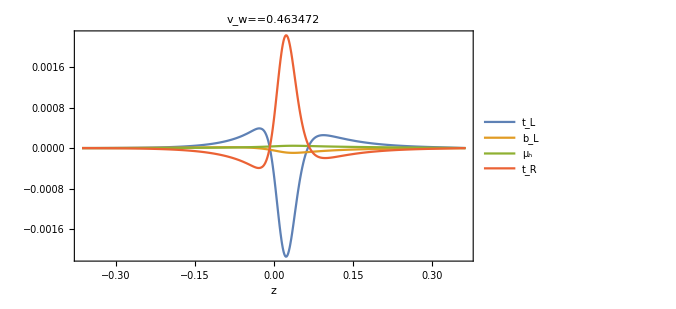
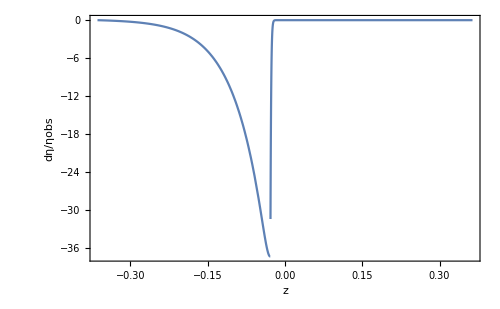
{173.32,{-Graphics-,-Graphics-,-2.39519}}

```mathematica
k0=-1;
MasterPars[k0]
Timing[MasterOutputVel[k0,540,500]]
```

```mathematica
(*i=3;MasterFunction[Tnlist[[i]],-vwlist[[i]],h0list[[i]],Lhlist[[i]],s0list[[i]],Lslist[[i]],dslist[[i]],1000]*)
```

```mathematica
BAULAM540=ParallelTable[Join[{vwlist[[i]]},MasterOutputVel[i,540,500]],{i,1,Length[Tnlist]}];
```

NIntegrate::maxp: 
   The integral failed to converge after 50000
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000305356 and 3.64896 10
     for the integral and error estimates.

NIntegrate::maxp: 
   The integral failed to converge after 50000
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000235924 and 2.50326 10
     for the integral and error estimates.

NIntegrate::maxp: 
   The integral failed to converge after 50000
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000617809 and 7.54719 10
     for the integral and error estimates.

NIntegrate::maxp: 
   The integral failed to converge after 50000
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000398041 and 5.26701 10
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::maxp: 
   The integral failed to converge after 50000
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000332736 and 4.28338 10
     for the integral and error estimates.

NIntegrate::maxp: 
   The integral failed to converge after 50000
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000272626 and 3.08718 10
     for the integral and error estimates.

NIntegrate::maxp: 
   The integral failed to converge after 50000
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000702104 and 8.33551 10
     for the integral and error estimates.

NIntegrate::maxp: 
   The integral failed to converge after 50000
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000529721 and 6.69317 10
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::maxp: 
   The integral failed to converge after 50000
     integrand evaluations. NIntegrate obtained 0.000992217 and 0.000011053
     for the integral and error estimates.

NIntegrate::maxp: 
   The integral failed to converge after 50000
                                                                         -6
     integrand evaluations. NIntegrate obtained 0.00077837 and 9.04572 10
     for the integral and error estimates.

NIntegrate::maxp: 
   The integral failed to converge after 50000
     integrand evaluations. NIntegrate obtained 0.00100062 and 0.0000111337
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::maxp: 
   The integral failed to converge after 50000
     integrand evaluations. NIntegrate obtained 0.00101759 and 0.0000113001
     for the integral and error estimates.

NIntegrate::maxp: 
   The integral failed to converge after 50000
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000880429 and 9.99133 10
     for the integral and error estimates.

NIntegrate::maxp: 
   The integral failed to converge after 50000
     integrand evaluations. NIntegrate obtained 0.000992217 and 0.000011053
     for the integral and error estimates.

NIntegrate::maxp: 
   The integral failed to converge after 50000
     integrand evaluations. NIntegrate obtained 0.0010091 and 0.0000112173
     for the integral and error estimates.

NIntegrate::maxp: 
   The integral failed to converge after 50000
     integrand evaluations. NIntegrate obtained 0.00104289 and 0.0000115486
     for the integral and error estimates.

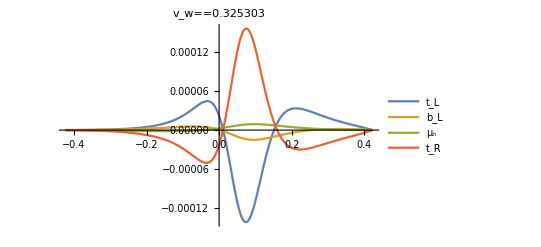
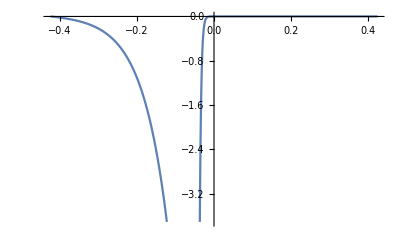
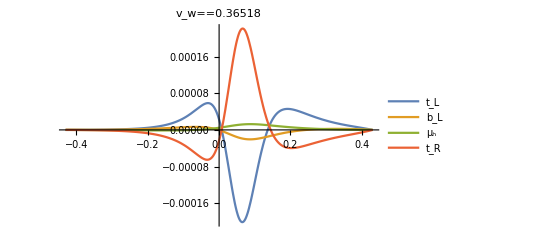
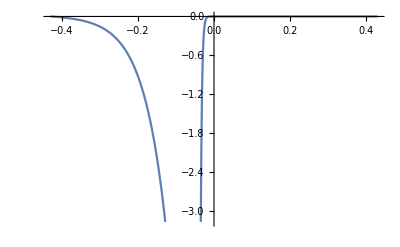
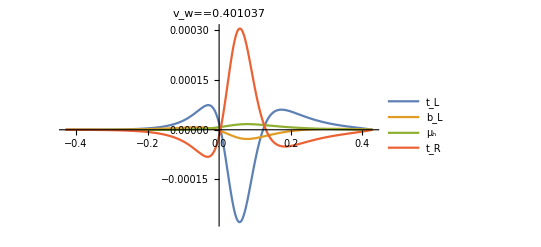
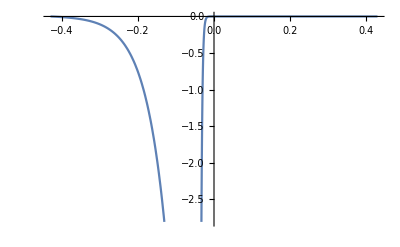
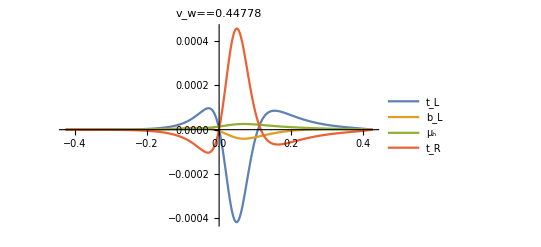
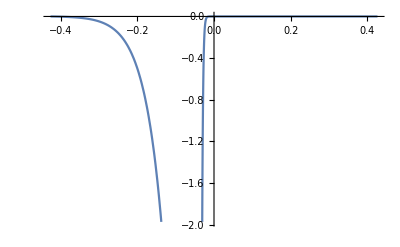
{{0.32998,-Graphics-,-Graphics-,-0.823821},{0.371708,-Graphics-,-Graphics-,-0.834869},{0.410233,-Graphics-,-Graphics-,-0.837885},{0.463559,-Graphics-,-Graphics-,-0.79814},{0.51974,-Graphics-,-Graphics-,-0.860713},{0.562252,-Graphics-,-Graphics-,-1.12199},{0.580475,-Graphics-,-Graphics-,-1.32234},{0.599279,-Graphics-,-Graphics-,-1.52254},{0.618538,-Graphics-,-Graphics-,-1.70817},{0.647985,-Graphics-,-Graphics-,-1.96408},{0.689448,-Graphics-,-Graphics-,-2.25751},{0.689448,-Graphics-,-Graphics-,-2.25751},{0.692829,-Graphics-,-Graphics-,-2.28006},{0.696514,-Graphics-,-Graphics-,-2.30299},{0.700141,-Graphics-,-Graphics-,-2.32599},{0.71155,-Graphics-,-Graphics-,-2.39519}}

```mathematica
BAULAM540
```

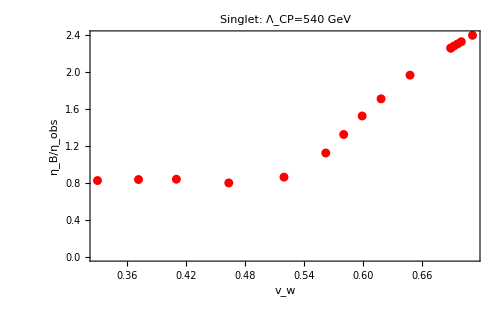

```mathematica
(*BAULAM540=Import["BAU_vw_LAM_1000.csv"];*)
BAUPlot1=ListPlot[Abs[BAULAM540[[All,{1,4}]]],FrameLabel->{"v_w","η_B/η_obs"},LabelStyle->Directive[Black,Bold],PlotStyle->Red,PlotLabel->"Singlet: Λ_CP=540 GeV"(*,PlotRange->{{vwdat[[1]]-0.01,vwdat[[-1]]+0.01},{-.1,.1}}*)]
```

```mathematica
Export["BAUPlot1.jpg",BAUPlot1]
```

BAUPlot1.jpg

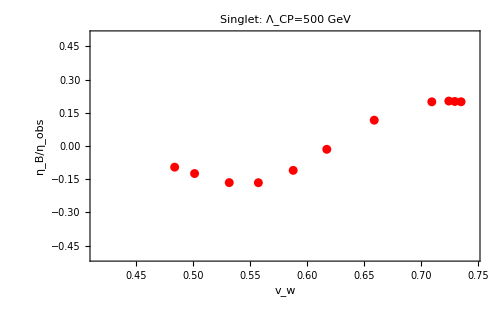

```mathematica
BAULAM500invGamma=Import["BAULAM500invGamma.csv"];ListPlot[BAULAM500invGamma,FrameLabel->{"v_w","η_B/η_obs"},LabelStyle->Directive[Black,Bold],PlotStyle->Red,PlotLabel->"Singlet: Λ_CP=500 GeV",PlotRange->{{vwdat[[1]]-0.01,vwdat[[-1]]+0.01},{-.5,.5}}]
```

```mathematica
BAULAM500=Table[MasterOutput[i,500],{i,1,Length[Tnlist]}];
```

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 1.90767×10^16 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained -5.06346×10^6 and 77868.6 for the integral and error estimates.

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 1.03252×10^9 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

General::stop: Further output of NDSolve::bvluc will be suppressed during this calculation.

NDSolve::berr: The scaled boundary value residual error of 6.7127 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

General::stop: Further output of NDSolve::berr will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.0000440428 and 1.15317×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.0000600431 and 1.50121×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Export["BAULAM500.csv",Transpose[{vwdat,Transpose[BAULAM500][[2]]/ηobs}]]
```

BAULAM500.csv